```mathematica
ResourceFunction["DarkMode"][False]
```

```mathematica
fn =FileNames[All, "/Users/erichegonzales/Projects/Wolfram/ProbabilityResearch/cbball_data"];
```

```mathematica
fn[[1]]
```

```mathematica
Length[fn]
```

```mathematica
game1 =Import[fn[[1]], "Dataset", "HeaderLines"-> 1]
```

```mathematica
i = 1;
possessionStatuses = {};
row = game1[[1]];
curr = row["possession_before"]
```

```mathematica
possessionStatuses
```

```mathematica
importScoreDiff[fn_]:=Module[{game},
game = Import[fn, "Dataset", "HeaderLines"-> 1];
Normal[game[All, "score_diff"]]]
```

```mathematica
scoreDiffs = importScoreDiff /@ fn
```

```mathematica
scoreDiffs =Drop[scoreDiffs , -1]
```

```mathematica
numRunsgetNumRunsof5
```

```mathematica
Total[{1, 2, 3}]
```

```mathematica
scoreDiff =Normal[game1[All, "score_diff"]]
scoreDiffd =Differences[scoreDiff]
```

```mathematica
sameDirectionQ[dir_, val_] := If[dir == "pos", NonNegative[val], NonPositive[val]]
oppDirection[dir_]:= If[dir == "pos", "neg", "pos"]
```

```mathematica
getNumRunsof5[scoreDiffd_]:=Module[{numRunsof5 =0, lengthCurrRun = 0, dir = RandomChoice[{"pos", "neg"}]},
Scan[
If[sameDirectionQ[dir,#], 
lengthCurrRun+= #; If[Abs[lengthCurrRun]>= 5, numRunsof5++; lengthCurrRun = 0],
lengthCurrRun = #; dir =  oppDirection[dir]
]&, 
scoreDiffd];
numRunsof5]
```

```mathematica
runsof5 = getNumRunsof5[Differences[#]] &/@ scoreDiffs
```

```mathematica
Total[runsof5]
```

```mathematica
scoreDiffds = Differences /@ scoreDiffs
```

```mathematica
counts = Counts[Flatten[scoreDiffds]]
ps = counts / Length[Flatten[scoreDiffds]]
```

```mathematica
RandomChoice[Values[ps]-> Keys[ps]]
```

```mathematica
streakBball[x_, choice_, dir_, dep_]:= If[x==>=2,RandomChoice[{pScore-dep,1-pScore+dep}-> {"score", "empty"}], RandomChoice[{1-pAgain, pAgain}-> {-1, 1}]]
```

```mathematica
Switch[x, 
GreaterEqual[2], ]
```

```mathematica
Switch[1,_Integer, "hi"]
```

### Pipeline

```mathematica
fn =FileNames[All, "/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23"][[;;-3]];
```

```mathematica
Length[fn]
```

36

```mathematica
fn
```

{/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401481155.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401481156.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401481157.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401481158.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401482883.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484515.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484516.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484517.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484518.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484519.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484644.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484645.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484646.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484981.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401484982.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485284.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485285.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485286.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485456.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485457.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485458.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485459.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401485460.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401488525.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401492761.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401492762.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401493458.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401493459.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401497508.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514254.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514255.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514329.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514330.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514331.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514332.csv,/Users/erichegonzales/Projects/Wolfram/Probability Research/cbball_data/03-01-23/401514336.csv}

```mathematica
testGames = Import[#, "Dataset", "HeaderLines"->1]&/@ fn;
```

```mathematica
getPossStatuses[game_]:=Module[{i, possStatuses,possStatus, row, curr, homeTeam, awayTeam, currTeam},
i = 1;
possStatuses = {};
row = game[[1]];
homeTeam = row[["home"]];
awayTeam = row[["away"]];
While[i<=Length[game],
curr = row[["possession_before"]];
If[curr == homeTeam, currTeam = "home", currTeam = "away"];
possStatus=currTeam<>"Empty";
While[row[["possession_before"]] == curr, 
If[row[["shot_outcome"]] == "made", possStatus = currTeam<>"Score"];
i += 1;
row = game[[i, All]];
];
AppendTo[possStatuses, possStatus]
];
possStatuses
]
```

```mathematica
testCloseGames = Select[testGames, #[[-1, "score_diff"]]<10&];
```

```mathematica
scoreDiffs = Flatten[Normal[#[[All, "score_diff"]]&/@testCloseGames]];
```

```mathematica
Length[scoreDiffs]
```

6740

```mathematica
gamePossStatuses = getPossStatuses/@testCloseGames;
```

```mathematica
n= Length[Flatten[gamePossStatuses]]
nHome =Length[Select[Flatten[gamePossStatuses], StringContainsQ[#, "home"]&]]
nAway =Length[Select[Flatten[gamePossStatuses], StringContainsQ[#, "away"]&]]
```

2821

1410

1411

```mathematica
homeCount = Count[gamePossStatuses, "homeScore", 2] ;
awayCount =Count[gamePossStatuses, "awayScore", 2];
homeECount = Count[gamePossStatuses, "homeEmpty", 2] ;
awayECount =Count[gamePossStatuses, "awayEmpty", 2] ;
pHome = homeCount/ n;
pAway = awayCount / n;
pHEmpty = homeECount / n;
pAEmpty = awayECount / n;
```

```mathematica
pHome
```

684/2821

```mathematica
pAway
```

680/2821

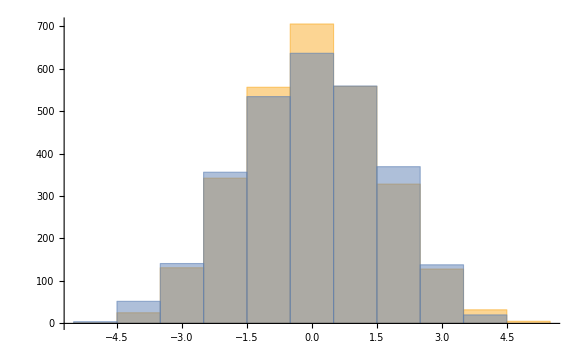

```mathematica
simHomePossStatuses = Table[RandomChoice[{homeCount / nHome, homeECount / nHome}->{1, 0}], nHome];
simAwayPossStatuses = 
Table[RandomChoice[{awayCount / nAway, awayECount / nAway}->{-1, 0}], nAway];
simPossStatusesHomeAway = Riffle[simHomePossStatuses, simAwayPossStatuses];
possStatuses10 = Map[If[# == "homeScore", 1, If [# == "awayScore", -1, 0]]&, Flatten[gamePossStatuses]];
(*ListLinePlot[Accumulate[possStatuses10]]
ListLinePlot[Accumulate[simPossStatusesHomeAway]]*)
diffsReal = Differences[Accumulate[possStatuses10], 1, 10];
diffsSim = Differences[Accumulate[simPossStatusesHomeAway], 1, 10];
(*ListLinePlot[diffsReal, PlotRange->{{0, 1000}, {-10, 9}}]
ListLinePlot[diffsSim, PlotRange->{{0, 1000},{-10, 9}}]*)
Histogram[{diffsReal, diffsSim}]
```

```mathematica
ListLinePlot[Differences[Accumulate[Flatten[gamePossStatuses]], 1, 10], PlotRange->{-10, 9}]
ListLinePlot[Differences[Accumulate[simPossStatuses], 1, 10], PlotRange->{-10, 9}]
```

-Graphics-

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[simPossStatuses].

Differences::listrp: List or SparseArray or structured array expected at position 1 in Differences[False,False,False].

ListLinePlot::lpn: Differences[Accumulate[simPossStatuses],1.,10.] is not a list of numbers or pairs of numbers.

ListLinePlot[Differences[Accumulate[simPossStatuses],1,10],PlotRange→{-10,9}]

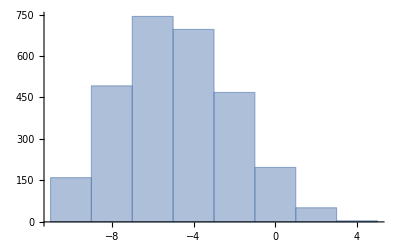

```mathematica
simPossStatuses = Table[RandomChoice[{pHome, 1-pHome}->{1, -1}], n];
Histogram[{Differences[Accumulate[Flatten[gamePossStatuses]], 1, 10],Differences[Accumulate[simPossStatuses], 1, 10]}]
```

5-7:HHHHHLHHLHHLHHHLHHHH
7-9:HHHHHLHHHHHHHHHHHHLH

```mathematica
seqs = {{1, 1}, {1, -1}, {-1, 1}, {-1,-1}}
```

```mathematica
{SequenceCount[Flatten[gamePossStatuses], {1, -1, 1, -1}] , SequenceCount[simPossStatuses, {1, -1, 1, -1}]}
```

```mathematica
BarChart[SequenceCount[Flatten[gamePossStatuses],#]&/@ seqs]
```

```mathematica
BarChart[SequenceCount[simPossStatuses,#]&/@ seqs]
```

### Score Diffs

```mathematica
scoreDiffs = Normal[#[[All, "score_diff"]]&/@testCloseGames];
```

```mathematica
scoreDiffsD = Differences/@ scoreDiffs;
```

```mathematica
scoreDiffsDLengths = Length/@scoreDiffsD
```

{320,334,427,278,348,314,397,345,297,290,341,322,332,332,339,357,351,370,308,318}

```mathematica
countsScoreDiffsD = Counts/@scoreDiffsD
```

{<|0→237,2→20,3→9,-2→20,-3→10,1→11,-1→13|>,<|-2→24,0→247,2→10,3→8,1→22,-3→10,-1→13|>,<|0→345,-2→12,2→14,-3→3,1→24,3→4,-1→25|>,<|0→200,-2→22,2→15,3→10,1→10,-1→16,-3→5|>,<|0→258,-2→24,2→15,3→12,1→20,-1→14,-3→5|>,<|1→16,-2→20,0→226,3→7,2→20,-3→7,-1→18|>,<|-3→12,0→298,2→22,-1→15,-2→18,3→8,1→24|>,<|0→266,1→25,-2→17,2→16,-1→10,-3→8,3→3|>,<|3→14,0→213,2→8,-2→18,1→20,-3→10,-1→13,-4→1|>,<|0→230,3→12,-2→11,-3→13,2→12,1→5,-1→7|>,<|-2→24,2→15,0→239,-3→10,1→26,3→11,-1→16|>,<|0→251,-1→8,-2→24,-3→8,2→11,3→10,1→10|>,<|0→250,-2→16,-3→10,2→24,-1→11,1→16,3→5|>,<|0→267,2→16,-2→13,3→8,-3→7,1→8,-1→13|>,<|0→242,3→13,-2→22,2→18,-3→9,1→13,-1→22|>,<|0→258,2→16,-2→20,3→10,-3→7,1→26,-1→20|>,<|0→267,2→21,1→18,-3→8,3→5,-2→17,-1→15|>,<|0→291,-2→24,2→17,-1→12,1→15,3→7,-3→4|>,<|2→17,0→235,1→22,-3→10,-2→13,3→4,-1→7|>,<|0→238,3→9,2→22,1→12,-2→14,-3→12,-1→11|>}

```mathematica
tot0 = Total[#[0]&/@ countsScoreDiffsD];
tot1 = Total[#[1]&/@ countsScoreDiffsD];
tot2 = Total[#[2]&/@ countsScoreDiffsD];
tot3 = Total[#[3]&/@ countsScoreDiffsD];
totN1 = Total[#[-1]&/@ countsScoreDiffsD];
totN2 = Total[#[-2]&/@ countsScoreDiffsD];
totN3 = Total[#[-3]&/@ countsScoreDiffsD];
```

```mathematica
tots = {tot0, tot1, tot2, tot3, totN1, totN2, totN3}
```

{5058,343,329,169,279,373,168}

```mathematica
n2 = Length[Flatten[scoreDiffsD]]
```

6720

```mathematica
gameLengths = Length/@ testCloseGames
```

{321,335,428,279,349,315,398,346,298,291,342,323,333,333,340,358,352,371,309,319}

```mathematica
weights = #/n2&/@ tots
```

{843/1120,49/960,47/960,169/6720,93/2240,373/6720,1/40}

```mathematica
simScoreDiffsD = Table[RandomChoice[weights->{0, 1, 2, 3, -1, -2, -3}], #]&/@ scoreDiffsDLengths;
```

```mathematica
Length/@simScoreDiffsD
```

{320,334,427,278,348,314,397,345,297,290,341,322,332,332,339,357,351,370,308,318}

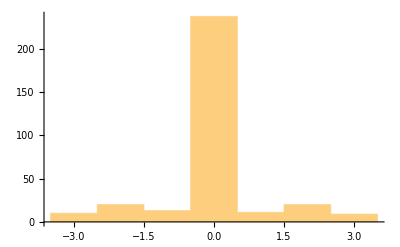

```mathematica
Histogram[scoreDiffsD[[1]]]
```

```mathematica
scoreDiffsDD = Differences[#, 1, 100]&/@scoreDiffsD;
```

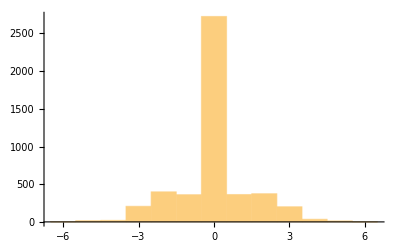

```mathematica
Histogram[Flatten[scoreDiffsDD]]
```

```mathematica
simScoreDiffsDD = Differences[#, 1, 100]&/@simScoreDiffsD;
```

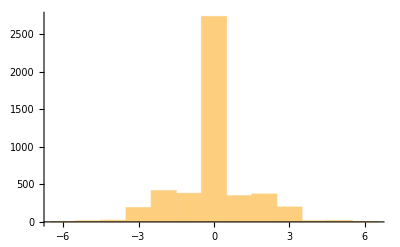

```mathematica
Histogram[Flatten[simScoreDiffsDD]]
```

```mathematica
Histogram[Flatten[scoreDiffsDD]]
```

-Graphics-